# Pendekatan Kuadrat Terkecil Terbobot Bulan Mulya Utama & Chalista Divia Maharani

### Kasus Kontinu

(Exercise Set 8.3, Plybon page 335)

Tentukan polinomial pendekatan kuadrat terkecil dari fungsi f(x)=ⅇ^-x pada interval [-1,1] dengan w(x) = 1. Dalam kasus ini, akan dicari polinomial pendekatan berderajat satu sampai empat.

```mathematica
f[x_]=ⅇ^-x
```

ⅇ^-x

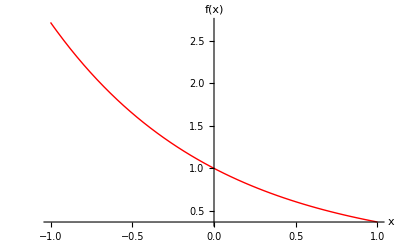

```mathematica
Fungsi=Plot[ⅇ^-x,{x,-1,1}, AxesLabel -> {"x","f(x)"},PlotStyle->{Red,Thick} ]
```

Polinomial Berderajat Satu

```mathematica
LeastSquares[({{∫_-1^1. 1ⅆx, ∫_-1^1. xⅆx}, {∫_-1^1. xⅆx, ∫_-1^1. x^2 ⅆx}}),({{∫_-1^1. ⅇ^-x ⅆx}, {∫_-1^1. x ⅇ^-x ⅆx}})]
```

{{1.1752},{-1.10364}}

Diperoleh a_0= 1.1752 dan a_1= -1.10364 sehingga diperoleh polinomial berderajat satu yaitu P_1(x)= 1.1752-1.10364x.

```mathematica
P1[x_]=1.1752-1.10364x
```

1.1752-1.10364 x

Berikut merupakan grafik polinomial pendekatan berderajat satu.

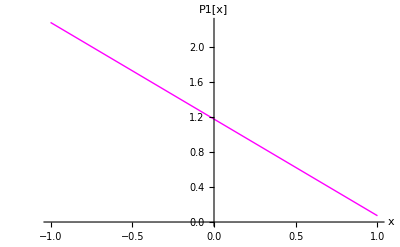

```mathematica
P1=Plot[{1.1752-1.10364x},{x,-1,1},AxesLabel-> {"x","P1[x]"},PlotStyle->{{Magenta,Thick}}]
```

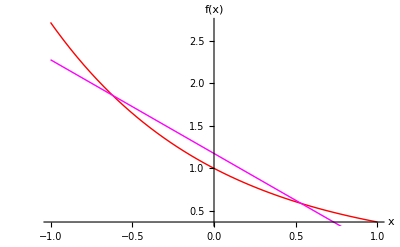

```mathematica
Show[{Fungsi,P1}]
```

Berikut merupakan grafik eror dari polinomial pendekatan berderajat satu.

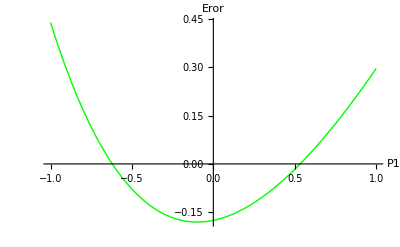

```mathematica
ErorP1=Plot[{ⅇ^-x-(1.1752-1.10364x)},{x,-1,1},AxesLabel->{"P1","Eror"}, PlotStyle->{Green, Thick}]
```

Polinomial Berderajat Dua

```mathematica
LeastSquares[({{∫_-1^1. 1ⅆx, ∫_-1^1. xⅆx, ∫_-1^1. x^2 ⅆx}, {∫_-1^1. xⅆx, ∫_-1^1. x^2 ⅆx, ∫_-1^1. x^3 ⅆx}, {∫_-1^1. x^2 ⅆx, ∫_-1^1. x^3 ⅆx, ∫_-1^1. x^4 ⅆx}}),({{∫_-1^1. ⅇ^-x ⅆx}, {∫_-1^1. x ⅇ^-x ⅆx}, {∫_-1^1 x^2 ⅇ^-x ⅆx}})]
```

{{0.996294},{-1.10364},{0.536722}}

```mathematica
Flatten[{{0.996294},{-1.10364},{0.536722}}]
```

{0.996294,-1.10364,0.536722}

Diperoleh a_0=0.996294, a_1=-1.10364, dan a_2=0.536722 sehingga diperoleh polinomial berderajat 2 yaitu P_2(x)=0.996294-1.10364x+0.536722 x^2.

```mathematica
P2[x_]=0.996294-1.10364x+0.536722 x^2
```

0.996294-1.10364 x+0.536722 x^2

Berikut merupakan grafik polinomial pendekatan berderajat dua.

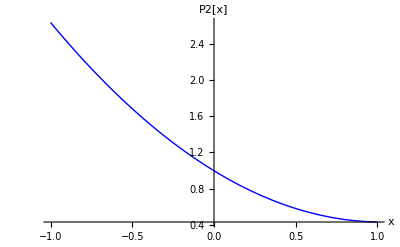

```mathematica
P2=Plot[{0.996294-1.10364 x+0.536722 x^2},{x,-1,1},AxesLabel-> {"x","P2[x]"},PlotStyle->{Blue,Thick}]
```

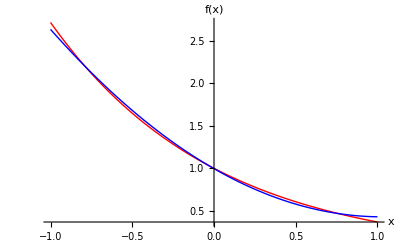

```mathematica
Show[{Fungsi,P2}]
```

Berikut merupakan grafik eror dari polinomial pendekatan berderajat dua.

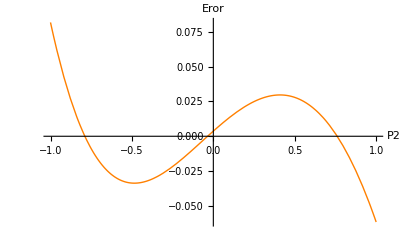

```mathematica
ErorP2=Plot[{ⅇ^-x-(0.996294-1.10364 x+0.536722 x^2)},{x,-1,1},AxesLabel->{"P2","Eror"}, PlotStyle->{Orange, Thick}]
```

Polinomial Berderajat Tiga

```mathematica
LeastSquares[({{∫_-1^1. 1ⅆx, ∫_-1^1. xⅆx, ∫_-1^1. x^2 ⅆx, ∫_-1^1. x^3 ⅆx}, {∫_-1^1. xⅆx, ∫_-1^1. x^2 ⅆx, ∫_-1^1. x^3 ⅆx, ∫_-1^1. x^4 ⅆx}, {∫_-1^1. x^2 ⅆx, ∫_-1^1. x^3 ⅆx, ∫_-1^1. x^4 ⅆx, ∫_-1^1. x^5 ⅆx}, {∫_-1^1. x^3 ⅆx, ∫_-1^1. x^4 ⅆx, ∫_-1^1. x^5 ⅆx, ∫_-1^1. x^6 ⅆx}}),({{∫_-1^1. ⅇ^-x ⅆx}, {∫_-1^1. x ⅇ^-x ⅆx}, {∫_-1^1. x^2 ⅇ^-x ⅆx}, {∫_-1^1. x^3 ⅇ^-x ⅆx}})]
```

{{0.996294},{-0.997955},{0.536722},{-0.176139}}

```mathematica
Flatten[{{0.996294},{-0.997955},{0.536722},{-0.176139}}]
```

{0.996294,-0.997955,0.536722,-0.176139}

Diperoleh a_0=0.996294, a_1=-0.997955, a_2=0.536722, dan a_3=-0.176139 sehingga diperoleh polinomial berderajat 3 yaitu P_3(x)=0.996294-0.997955x+0.536722 x^2-0.176139 x^3.

```mathematica
P3[x_]=0.996294-0.997955x+0.536722 x^2-0.176139 x^3
```

0.996294-0.997955 x+0.536722 x^2-0.176139 x^3

Berikut merupakan grafik polinomial pendekatan berderajat tiga.

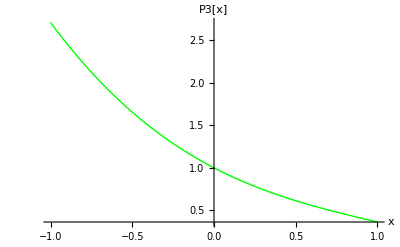

```mathematica
P3=Plot[{0.996294-0.997955x+0.536722 x^2-0.176139 x^3},{x,-1,1},AxesLabel-> {"x","P3[x]"},PlotStyle->{Green,Thick}]
```

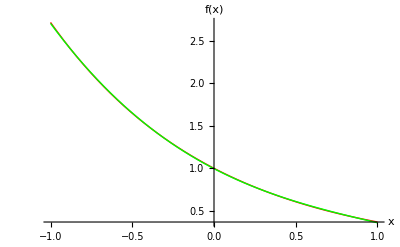

```mathematica
Show[{Fungsi,P3}]
```

Berikut merupakan grafik eror dari polinomial pendekatan berderajat tiga.

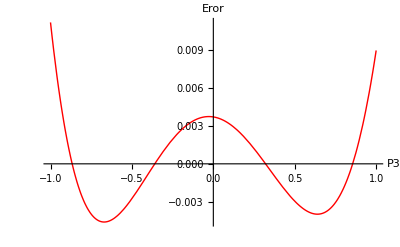

```mathematica
ErorP3=Plot[{ⅇ^-x-(0.996294-0.997955x+0.536722 x^2-0.176139 x^3)},{x,-1,1},AxesLabel->{"P3","Eror"}, PlotStyle->{Red, Thick}]
```

Polinomial Berderajat Empat

```mathematica
LeastSquares[({{∫_-1^1. 1ⅆx, ∫_-1^1. xⅆx, ∫_-1^1. x^2 ⅆx, ∫_-1^1. x^3 ⅆx, ∫_-1^1. x^4 ⅆx}, {∫_-1^1. xⅆx, ∫_-1^1. x^2 ⅆx, ∫_-1^1. x^3 ⅆx, ∫_-1^1. x^4 ⅆx, ∫_-1^1. x^5 ⅆx}, {∫_-1^1. x^2 ⅆx, ∫_-1^1. x^3 ⅆx, ∫_-1^1. x^4 ⅆx, ∫_-1^1. x^5 ⅆx, ∫_-1^1. x^6 ⅆx}, {∫_-1^1. x^3 ⅆx, ∫_-1^1. x^4 ⅆx, ∫_-1^1. x^5 ⅆx, ∫_-1^1. x^6 ⅆx, ∫_-1^1. x^7 ⅆx}, {∫_-1^1. x^4 ⅆx, ∫_-1^1. x^5 ⅆx, ∫_-1^1. x^6 ⅆx, ∫_-1^1. x^7 ⅆx, ∫_-1^1. x^8 ⅆx}}),({{∫_-1^1. ⅇ^-x ⅆx}, {∫_-1^1. x ⅇ^-x ⅆx}, {∫_-1^1. x^2 ⅇ^-x ⅆx}, {∫_-1^1. x^3 ⅇ^-x ⅆx}, {∫_-1^1. x^4 ⅇ^-x ⅆx}})]
```

{{1.00003},{-0.997955},{0.499352},{-0.176139},{0.0435974}}

Diperoleh a_0=1.00003, a_1=-0.997955, a_2=0.499352, a_3=-0.176139, dan a_4=-89.8263 sehingga diperoleh polinomial berderajat 4 yaitu P_4(x)=1.00003-0.997955x+0.499352 x^2-0.176139 x^3+0.0435974 x^4.

```mathematica
P4[x_]=1.00003-0.997955x+0.499352 x^2-0.176139 x^3+0.0435974 x^4
```

1.00003-0.997955 x+0.499352 x^2-0.176139 x^3+0.0435974 x^4

Berikut merupakan grafik polinomial pendekatan berderajat empat.

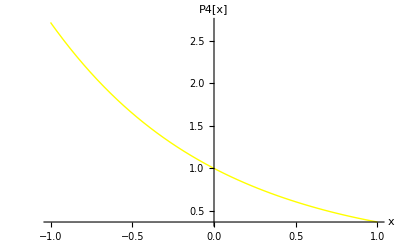

```mathematica
P4=Plot[{1.00003-0.997955x+0.499352 x^2-0.176139 x^3+0.0435974 x^4},{x,-1,1},AxesLabel-> {"x","P4[x]"},PlotStyle->{Yellow,Thick}]
```

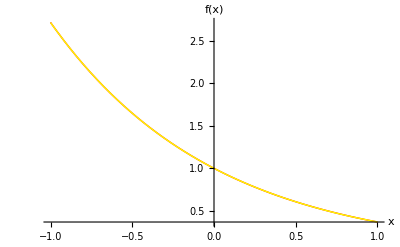

```mathematica
Show[{Fungsi,P4}]
```

Berikut merupakan grafik eror dari polinomial pendekatan berderajat empat.

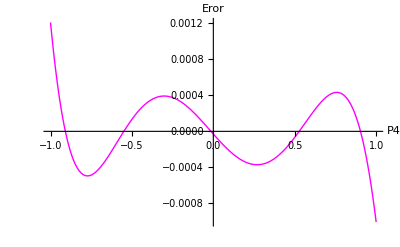

```mathematica
ErorP4=Plot[{ⅇ^-x-(1.00003-0.997955x+0.499352 x^2-0.176139 x^3+0.0435974 x^4)},{x,-1,1},AxesLabel->{"P4","Eror"}, PlotStyle->{Magenta, Thick}]
```

Berikut merupakan grafik gabungan polinomial pendekatan diatas.

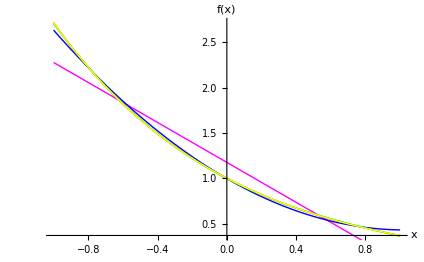

```mathematica
Show[{Fungsi,P1,P2,P3,P4}]
```

Berikut merupakan grafik gabungan distribusi eror diatas.

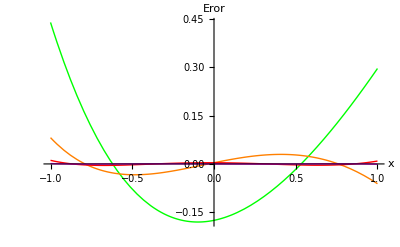

```mathematica
Show[{ErorP1,ErorP2,ErorP3,ErorP4},AxesLabel->{"x","Eror"}]
```